# dual method for 2D penrose (5-fold)

Let’s first define basis vectors

```mathematica
(*this function finds intersection point of two grid lines, where e_i denotes star vector, and n_i denotes line number*)
FindIntersection[{n1_,e1_},{n2_,e2_},{n3_,e3_}]:=Module[
{p1,p2,p3},
p1=n1*e1;
p2=n2*e2;
p3=n3*e3;
1/Det[{e1,e2,e3}]*
((p1.e1)Cross[e2,e3]+(p2.e2)Cross[e3,e1]+(p3.e3)Cross[e1,e2])
]
```

```mathematica
a=2Pi/5;
r1={1,0,0};
r2={Cos[a],Sin[a],0};
r3={Cos[2a],Sin[2a],0};
r4={Cos[3a],Sin[3a],0}
vertices={r1,r2,r3,r4};
basis =Graphics[Arrow[{{0,0},#}]&/@vertices[[All,{1,2}]],Axes->True];
```

{1/4 (-1-√5),-√(5/8-(√5)/8),0}

```mathematica
a1=1;
a2=1;
a3=1;
a4=1;
spacing={a1,a2,a3,a4};
```

```mathematica
pts=Table[FindIntersection[{m,a},{n,b},{0,{0,0,1}}],{m,Range[-5,5]},{n,Range[-5,5]},{a,vertices},{b,vertices}];
pts=Flatten[pts[[All,All,{1,2}]],3];
Length[pts]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating (1/4 - √5/4)\ (-5\ (5/8 + √5/8) - 5/16\ (-1 + √5)^2) + (-1/4 + √5/4)\ (-5\ (5/8 + √5/8) - 5/16\ (-1 + √5)^2).

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating (-1/4 - √5/4)\ (-5/16\ (-1 - Power[« 2 »])^2 - 5\ (5/8 - √5/8)) + (1/4 + √5/4)\ (-5/16\ (-1 - Power[« 2 »])^2 - 5\ (5/8 - √5/8)).

General::stop: Further output of N :: meprec will be suppressed during this calculation.

968

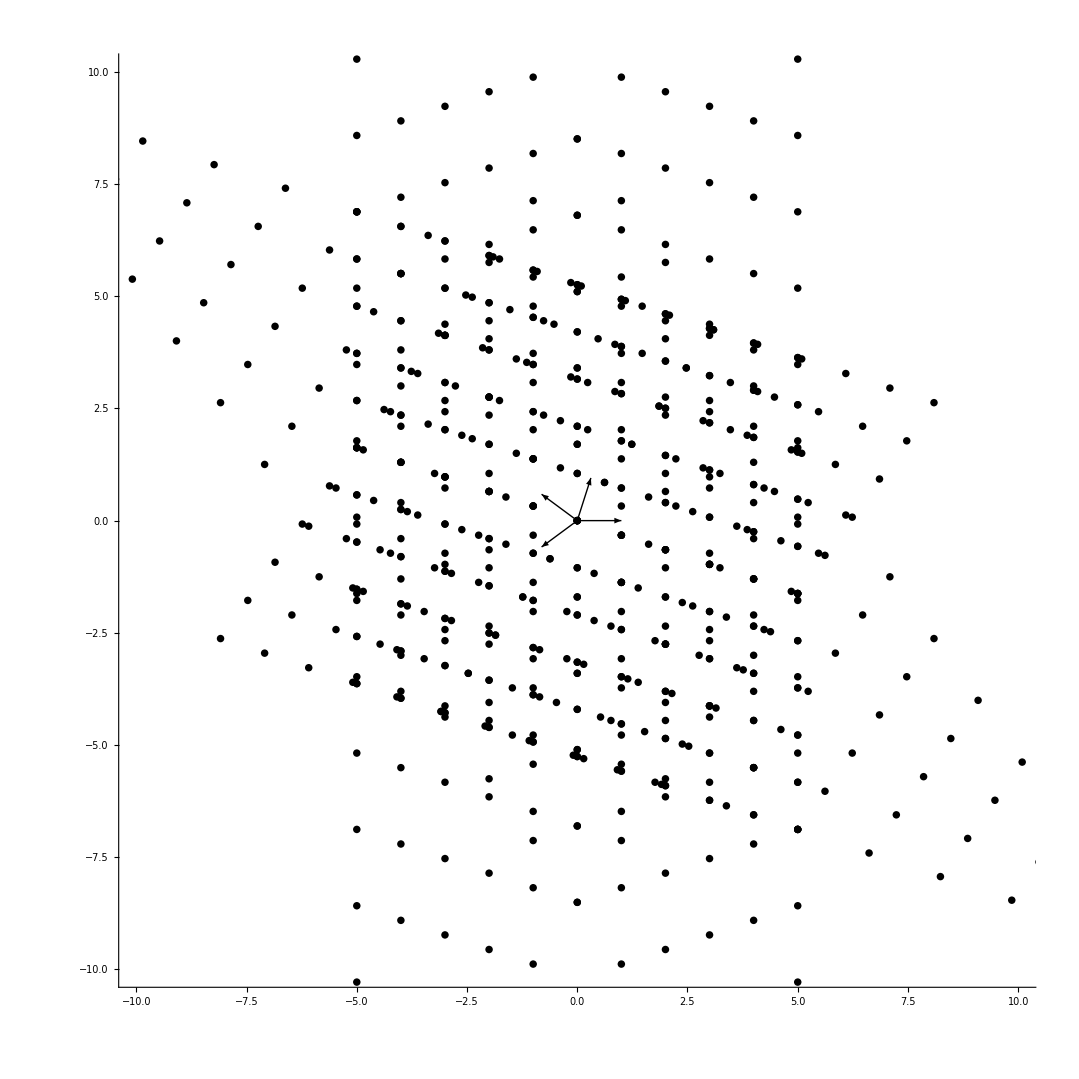

```mathematica
Show[basis,
Graphics[{PointSize[0.005],Point[Cases[pts,{_?NumericQ,_?NumericQ,0}][[All,{1,2}]]]}]
, AspectRatio->1,PlotRange->{{-10,10},{-10,10}}]
```